```mathematica
list = Import[NotebookDirectory[]<>"/res/out_1.5_2.0.txt","Table"];
Length[list]
len=Length[list[[1]]]
```

250

1001

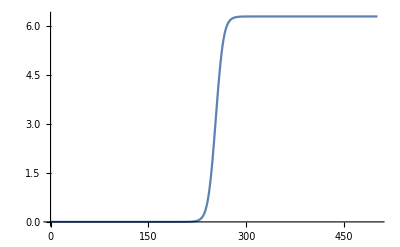

```mathematica
ListLinePlot[list[[10]],PlotRange->All]
```

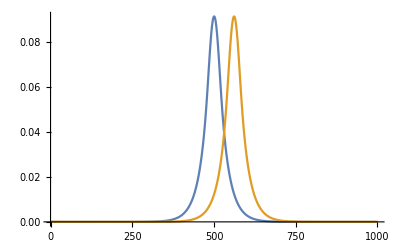

```mathematica
ListLinePlot[{Differences[list[[1]]],Differences[list[[-1]]]},PlotRange->Full]
```

```mathematica
f1=NIntegrate[Interpolation[Differences[list[[1]]]][x],{x,1,len-1}]
f2=NIntegrate[Interpolation[Differences[list[[-1]]]][x],{x,1,len-1}]
(f2-f1)/f1
```

6.283

6.28331

0.0000496243